```mathematica
daljica=Daljica[{-1,1},{3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
Dolzina[daljica]
```

2 √5

```mathematica
Dolzina[Daljica[AA_,BB_]]:=Norm[BB-AA]
```

```mathematica
Slika[Daljica[AA_,BB_]]:= Line[{AA,BB}]
```

```mathematica
Slika[daljica]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Clear[Narisi]
```

```mathematica
ClearAll[Narisi]
Narisi[d__Daljica]:=Graphics[Map[Slika,List[d]]]
```

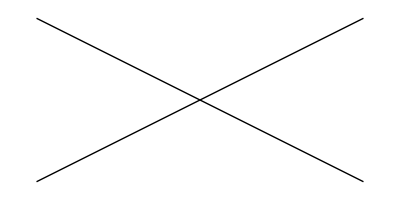

```mathematica
Narisi[daljica,b]
```

```mathematica
ClearAll[EnacbaNosilke,x,y]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]]:=Module[{x1,y1,x2,y2},
{x1,y1}=AA;
{x2,y2}=BB;
k= (y2-y1)/(x2-x1);
n=n/.First[Solve[y1==k*x1+n,n]];
y==k*x+n]
```

```mathematica
EnacbaNosilke[daljica]
```

y==1/2-x/2

```mathematica
b=Daljica[{-1,-1},{3,1}]
```

Daljica[{-1,-1},{3,1}]

```mathematica
ClearAll[Presek,s,r,b,daljica]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{resitev},
resitev=Solve[{AA+r(BB-AA)==CC+s(DD-CC),r≥0,s≤1,s≥0,r<=1},{r,s}]
]
```

```mathematica
Presek[daljica,b]
```

{{r→1/2,s→1/2}}